## C-Phase with KLM

```mathematica
B[θ_,ϕ_]:={{Cos[θ],-ⅇ^(+ⅈ ϕ)Sin[θ]},{+ⅇ^(-ⅈ ϕ)Sin[θ],Cos[θ]}};
θ1=π/8; ϕ1=0;
θ2=65.5302/180 π; ϕ2=0;
θ3=-π/8; ϕ3=0;
ϕ4=π;
(*η=1;*)
```

### after 50-50 Beam splitter on the left

```mathematica
{t10,b10}=B[π/4,0].{t11,b11};
```

### top

#### after Beam splitter 1 ( coupling modes 2 and 3)

```mathematica
{t21,t31}=B[θ1,ϕ1].{t22,t32};
t11=ⅇ^(-ⅈ ϕ4)t12;
```

#### after Beam splitter 2 (coupling modes 1 and 2)

```mathematica
{t12,t22}=B[θ2,ϕ2].{t13,t23};
t32=t33;
```

#### after Beam splitter 3 (coupling modes 2 and 3)

```mathematica
{t23,t33}=B[θ3,ϕ3].{t24,t34};
t13=t14;
```

#### Inefficient detectors

```mathematica
{t24,t2vac}={{√η,ⅈ √(1-η)},{+ⅈ √(1-η),η}}.{t25,t2dump};
{t34,t3vac}={{√η,ⅈ √(1-η)},{+ⅈ √(1-η),η}}.{t35,t3dump};
t14=t15;
```

### bottom

#### after Beam splitter 1 ( coupling modes 2 and 3)

```mathematica
{b21,b31}=B[θ1,ϕ1].{b22,b32};
b11=ⅇ^(-ⅈ ϕ4)b12;
```

#### after Beam splitter 2 (coupling modes 1 and 2)

```mathematica
{b12,b22}=B[θ2,ϕ2].{b13,b23};
b32=b33;
```

#### after Beam splitter 3 (coupling modes 2 and 3)

```mathematica
{b23,b33}=B[θ3,ϕ3].{b24,b34};
b13=b14;
```

#### Inefficient detectors

```mathematica
{b24,b2vac}={{√η,ⅈ √(1-η)},{ⅈ √(1-η),η}}.{b25,b2dump};
{b34,b3vac}={{√η,ⅈ √(1-η)},{ⅈ √(1-η),η}}.{b35,b3dump};
b14=b15;
```

### after 50-50 Beam splitter on the right

```mathematica
{t15,b15}=B[-π/4,0].{t16,b16};
```

### Operation

```mathematica
creationops=FullSimplify[CoefficientList[CoefficientList[(α+β t10)(γ+b10 δ)t21 b21,{t35,b35,t25,b25}][[1,1,2,2]],{t2dump,t3dump,b2dump,b3dump,t16,b16},{3,3,3,3,2,2}]];
fockstate=Table[√((i-1)!(j-1)!(k-1)!(l-1)!(m-1)!(n-1)!)creationops[[i,j,k,l,m,n]],{i,1,3},{j,1,3},{k,1,3},{l,1,3},{m,1,2},{n,1,2}];

P=Map[Abs[#]^2&,fockstate,{6}];
```

```mathematica
Total[P[[1,1,1,1]],2]
```

0.0625 Abs[α γ η]^2+0.0625 ⅇ^(-2 Im[ϕT]) Abs[√(1-α^2) γ η]^2+0.0625 ⅇ^(-2 Im[ϕC]) Abs[α √(1-γ^2) η]^2+0.0625 ⅇ^(-2 Im[ϕC]-2 Im[ϕT]) Abs[√(1-α^2) √(1-γ^2) η]^2

```mathematica
F[η_,α_,γ_,ϕT_,ϕC_]=Module[{},
β=√(1-α^2)ⅇ^(ⅈ ϕT);
δ=√(1-γ^2)ⅇ^(ⅈ ϕC);
Total[P[[1,1,1,1]],2]/Total[P,6]
];
```

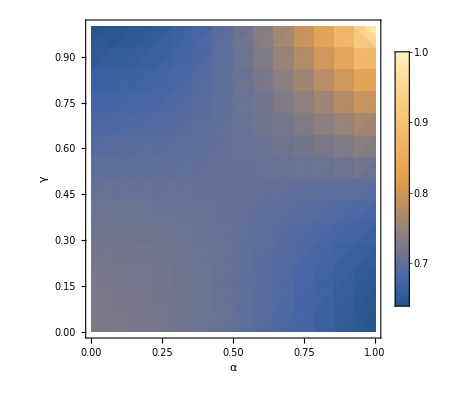

```mathematica
DensityPlot[F[0.80,α,γ,0,0],{α,0,1},{γ,0,1},PlotLegends->Automatic,PlotRange->{0,1},LabelStyle->Large,FrameLabel->Automatic]
```

### Average Fidelity

```mathematica
AvF[η_]:=N[1/(2π)^2 NIntegrate[F[η,α,γ,ϕT,ϕC],{α,0,1},{γ,0,1},{ϕT,0,2π},{ϕC,0,2π}]];
```

```mathematica
AvF[0.6]
```

0.503619

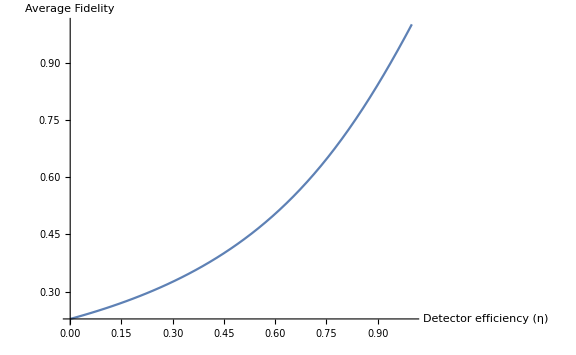

```mathematica
Plot[AvF[η],{η,0,1},PlotRange->Full,LabelStyle->Large,AxesLabel->{"Detector efficiency (η)","Average Fidelity"},ImageSize->Large,RotateLabel->True]
```